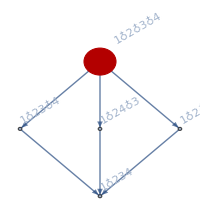
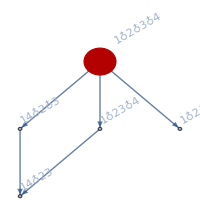
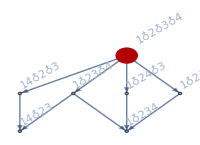
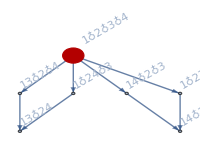
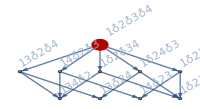
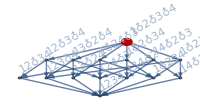
2→{{-Graphics-,62}}
3→{{-Graphics-,90}}
4→{{-Graphics-,16},{-Graphics-,12}}
5→{{-Graphics-,50},{-Graphics-,60}}
6→{}
7→{{-Graphics-,84},{-Graphics-,21}}
8→{}
9→{}
10→{{-Graphics-,60}}
11→{}
12→{}
13→{}
14→{}
15→{{-Graphics-,15}}

```mathematica
With[{all=allGraphs4,allKeys=allGraphs4AtomKeys},
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[Keys[all],With[{vars=ListofVars[all[#,"colofour"]]},Length[vars]==n&&MemberQ[vars,var]]&]},

Map[Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200]&,interest]
]
],
{k,allKeys}
]],IsomorphicGraphQ],
{n,2,15}], TableDirections->Column, TableDepth->1],{n,k}]
]
```

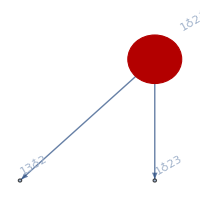
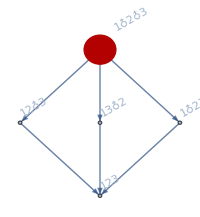
2→{{-Graphics-,12}}
3→{{-Graphics-,9}}
4→{}
5→{{-Graphics-,5}}

```mathematica
With[{all=allGraphs3,allKeys=allGraphs3AtomKeys},
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[Keys[all],With[{vars=ListofVars[all[#,"colofour"]]},Length[vars]==n&&MemberQ[vars,var]]&]},

Map[Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200]&,interest]
]
],
{k,allKeys}
]],IsomorphicGraphQ],
{n,2,5}], TableDirections->Column, TableDepth->1],{n,k}]
]
```

```mathematica
With[{all=allGraphs2,allKeys=allGraphs2AtomKeys},
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[Keys[all],With[{vars=ListofVars[all[#,"colofour"]]},Length[vars]==n&&MemberQ[vars,var]]&]},

Map[Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200]&,interest]
]
],
{k,allKeys}
]],IsomorphicGraphQ],
{n,2,5}], TableDirections->Column, TableDepth->1],{n,k}]
]
```

2→{{-Graphics-,2}}
3→{}
4→{}
5→{}

```mathematica
With[{all=allGraphs6,allAtoms=allGraphs6AtomKeys,vertices=6},
Block[
{lessKeys=Sort[Select[Keys[all],VertexCount[all[#,"graph"]]==vertices&]],byLength=Association[],l},
Table[byLength[i]={},
{i,Length[allAtoms]}
];
Table[
l=Length[ListofVars[all[k,"colofour"]]];
byLength[l]=Append[byLength[l],k]
,
{k,lessKeys}
];
Print[Table[
{k,Length[byLength[k]]}
,
{k,Length[allAtoms]}
]
];
Interrupt[];
Monitor[
TableForm[
Table[
n->Tally[Flatten[
Table[
With[{var=all[k,"colofour"]},
With[{interest=Select[byLength[n],With[{vars=ListofVars[all[#,"colofour"]]},MemberQ[vars,var]]&]},

Map[{Graph[FormulaGraphReverse2[all[#,"colofour"]],GraphHighlight->{var},VertexSize->{var->Large},ImageSize->200],PlanarGraphQ[all[#,"graph"]],#}&,interest]
]
],

{k,allAtoms}
],1],IsomorphicGraphQ[#1[[1]],#2[[1]]]&&#1[[2]]==#2[[2]]&],
{n,2,Length[allAtoms]}], TableDirections->Column, TableDepth->1],{n,k}]
]
]
```

{{1,1},{2,15},{3,60},{4,105},{5,230},{6,186},{7,585},{8,435},{9,390},{10,1140},{11,492},{12,720},{13,1320},{14,405},{15,1275},{16,990},{17,1620},{18,60},{19,360},{20,2640},{21,315},{22,1440},{23,900},{24,360},{25,790},{26,15},{27,2700},{28,0},{29,630},{30,1995},{31,0},{32,180},{33,0},{34,1090},{35,300},{36,0},{37,2160},{38,360},{39,0},{40,360},{41,60},{42,1080},{43,90},{44,0},{45,60},{46,0},{47,1140},{48,0},{49,0},{50,0},{51,72},{52,1296},{53,0},{54,405},{55,0},{56,0},{57,0},{58,0},{59,0},{60,240},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,1080},{68,0},{69,0},{70,45},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,20},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,435},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,0},{98,0},{99,0},{100,0},{101,0},{102,0},{103,0},{104,0},{105,0},{106,0},{107,0},{108,0},{109,0},{110,0},{111,0},{112,0},{113,0},{114,105},{115,0},{116,0},{117,0},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,15},{152,0},{153,0},{154,0},{155,0},{156,0},{157,0},{158,0},{159,0},{160,0},{161,0},{162,0},{163,0},{164,0},{165,0},{166,0},{167,0},{168,0},{169,0},{170,0},{171,0},{172,0},{173,0},{174,0},{175,0},{176,0},{177,0},{178,0},{179,0},{180,0},{181,0},{182,0},{183,0},{184,0},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,0},{195,0},{196,0},{197,0},{198,0},{199,0},{200,0},{201,0},{202,0},{203,1}}

$Aborted

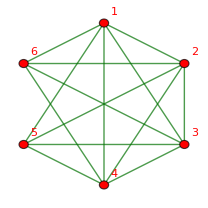

```mathematica
allGraphs6[7174452,"graph"]
```

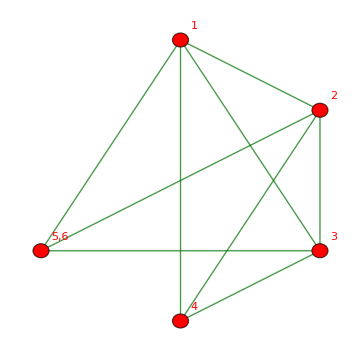

```mathematica
allGraphs6[7174442,"graph"]
```